Appendix

Question 2:
a.) Explain why the graphs of lnx1[t] and lnx2[t] should be approximately straight lines with slopes equal to λ1 and intercepts lnαv11 and lnαv21, respectively. Thus estimate of λ1, αv11 and αv21 may be obtained by fitting straight lines to the data lnx1*[tn] and lnx2*[tn] corresponding to values of tn, where the graphs of the logarithms of the data are approximately linear.

```mathematica
x1andx2data = {{0,0.623,0},{7.143,0.374,0.113},{14.286,0.249,0.151},{21.429,0.183,0.157},{28.571,0.145,0.150},{35.714,0.120,0.137},{42.857,0.103,0.124},{50,0.089,0.110},{57.143,0.078,0.098},{64.286,0.068,0.087},{71.429,0.060,0.077},{78.571,0.053,0.068},{85.714,0.047,0.060},{92.857,0.041,0.053},{100,0.037,0.047}}
```

{{0,0.623,0},{7.143,0.374,0.113},{14.286,0.249,0.151},{21.429,0.183,0.157},{28.571,0.145,0.15},{35.714,0.12,0.137},{42.857,0.103,0.124},{50,0.089,0.11},{57.143,0.078,0.098},{64.286,0.068,0.087},{71.429,0.06,0.077},{78.571,0.053,0.068},{85.714,0.047,0.06},{92.857,0.041,0.053},{100,0.037,0.047}}

```mathematica
Grid[x1andx2data]
```

0 | 0.623 | 0
7.143 | 0.374 | 0.113
14.286 | 0.249 | 0.151
21.429 | 0.183 | 0.157
28.571 | 0.145 | 0.15
35.714 | 0.12 | 0.137
42.857 | 0.103 | 0.124
50 | 0.089 | 0.11
57.143 | 0.078 | 0.098
64.286 | 0.068 | 0.087
71.429 | 0.06 | 0.077
78.571 | 0.053 | 0.068
85.714 | 0.047 | 0.06
92.857 | 0.041 | 0.053
100 | 0.037 | 0.047

```mathematica
ReplacePart[%45,1->Prepend[First[%45],{"Time (minutes)","x1 (mg/mL)","x2 (mg/mL)"}]]
```

Time (minutes) | x1 (mg/mL) | x2 (mg/mL)
0 | 0.623 | 0
7.143 | 0.374 | 0.113
14.286 | 0.249 | 0.151
21.429 | 0.183 | 0.157
28.571 | 0.145 | 0.15
35.714 | 0.12 | 0.137
42.857 | 0.103 | 0.124
50 | 0.089 | 0.11
57.143 | 0.078 | 0.098
64.286 | 0.068 | 0.087
71.429 | 0.06 | 0.077
78.571 | 0.053 | 0.068
85.714 | 0.047 | 0.06
92.857 | 0.041 | 0.053
100 | 0.037 | 0.047

```mathematica
Insert[%47,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

Time (minutes) | x1 (mg/mL) | x2 (mg/mL)
0 | 0.623 | 0
7.143 | 0.374 | 0.113
14.286 | 0.249 | 0.151
21.429 | 0.183 | 0.157
28.571 | 0.145 | 0.15
35.714 | 0.12 | 0.137
42.857 | 0.103 | 0.124
50 | 0.089 | 0.11
57.143 | 0.078 | 0.098
64.286 | 0.068 | 0.087
71.429 | 0.06 | 0.077
78.571 | 0.053 | 0.068
85.714 | 0.047 | 0.06
92.857 | 0.041 | 0.053
100 | 0.037 | 0.047

```mathematica
Insert[%47,{Background->{None,{GrayLevel[0.7],{White}}},Dividers->{Black,{2->Black}},Frame->True,Spacings->{2,{2,{0.7},2}}},2]
```

```mathematica
x1data = {{0,0.623},{7.143,0.374},{14.286,0.249},{21.429,0.183},{28.571,0.145},{35.714,0.120},{42.857,0.103},{50,0.089},{57.143,0.078},{64.286,0.068},{71.429,0.060},{78.571,0.053},{85.714,0.047},{92.857,0.041},{100,0.037}}
```

{{0,0.623},{7.143,0.374},{14.286,0.249},{21.429,0.183},{28.571,0.145},{35.714,0.12},{42.857,0.103},{50,0.089},{57.143,0.078},{64.286,0.068},{71.429,0.06},{78.571,0.053},{85.714,0.047},{92.857,0.041},{100,0.037}}

```mathematica
x2data={{0,0},{7.143,0.113},{14.286,0.151},{21.429,0.157},{28.571,0.150},{35.714,0.137},{42.857,0.124},{50,0.110},{57.143,0.098},{64.286,0.087},{71.429,0.077},{78.571,0.068},{85.714,0.060},{92.857,0.053},{100,0.047}}
```

{{0,0},{7.143,0.113},{14.286,0.151},{21.429,0.157},{28.571,0.15},{35.714,0.137},{42.857,0.124},{50,0.11},{57.143,0.098},{64.286,0.087},{71.429,0.077},{78.571,0.068},{85.714,0.06},{92.857,0.053},{100,0.047}}

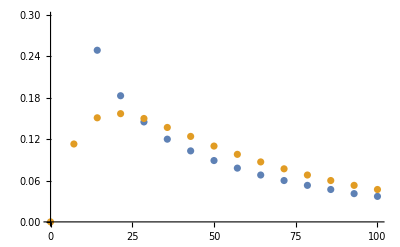

```mathematica
ListPlot[{x1data,x2data}]
```

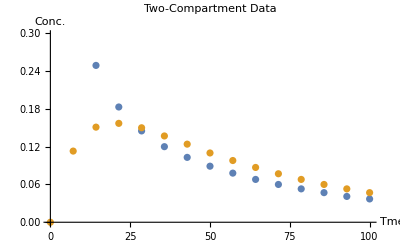

```mathematica
Show[%50,AxesLabel->{HoldForm[Tme],RawBoxes[RowBox[{"Conc","."}]]},PlotLabel->HoldForm[Two-Compartment Data],LabelStyle->{GrayLevel[0]}]
```

```mathematica
logx1data = {{0,Log[0.623]},{7.143,Log[0.374]},{14.286,Log[0.249]},{21.429,Log[0.183]},{28.571,Log[0.145]},{35.714,Log[0.120]},{42.857,Log[0.103]},{50,Log[0.089]},{57.143,Log[0.078]},{64.286,Log[0.068]},{71.429,Log[0.060]},{78.571,Log[0.053]},{85.714,Log[0.047]},{92.857,Log[0.041]},{100,Log[0.037]}}
```

{{0,-0.473209},{7.143,-0.983499},{14.286,-1.3903},{21.429,-1.69827},{28.571,-1.93102},{35.714,-2.12026},{42.857,-2.27303},{50,-2.41912},{57.143,-2.55105},{64.286,-2.68825},{71.429,-2.81341},{78.571,-2.93746},{85.714,-3.05761},{92.857,-3.19418},{100,-3.29684}}

```mathematica
logx2data={{0,Log[0]},{7.143,Log[0.113]},{14.286,Log[0.151]},{21.429,Log[0.157]},{28.571,Log[0.150]},{35.714,Log[0.137]},{42.857,Log[0.124]},{50,Log[0.110]},{57.143,Log[0.098]},{64.286,Log[0.087]},{71.429,Log[0.077]},{78.571,Log[0.068]},{85.714,Log[0.060]},{92.857,Log[0.053]},{100,Log[0.047]}}
```

{{0,-∞},{7.143,-2.18037},{14.286,-1.89048},{21.429,-1.85151},{28.571,-1.89712},{35.714,-1.98777},{42.857,-2.08747},{50,-2.20727},{57.143,-2.32279},{64.286,-2.44185},{71.429,-2.56395},{78.571,-2.68825},{85.714,-2.81341},{92.857,-2.93746},{100,-3.05761}}

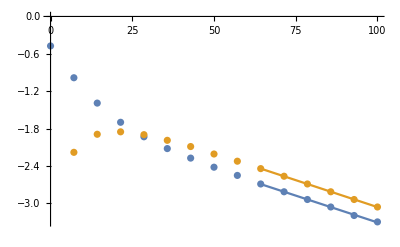

```mathematica
Show[ListPlot[{logx1data,logx2data}],Plot[{x1lineλ1,x2lineλ1},{t,64.286,100}]]
```

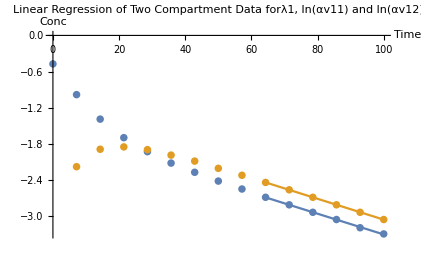

```mathematica
Show[%12,AxesLabel->{HoldForm[Time],HoldForm[Conc]},PlotLabel->RawBoxes[RowBox[{RowBox[{"Linear"," ","Regression"," ","of"," ","Two"," ","Compartment"," ","Data"," ","forλ1"}],","," ",RowBox[{"ln",RowBox[{"(","αv11",")"}]," ","and"," ","ln",RowBox[{"(","αv12",")"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
SubGroupLogx1Dataλ1 = {{64.286,Log[0.068]},{71.429,Log[0.060]},{78.571,Log[0.053]},{85.714,Log[0.047]},{92.857,Log[0.041]},{100,Log[0.037]}}
```

{{64.286,-2.68825},{71.429,-2.81341},{78.571,-2.93746},{85.714,-3.05761},{92.857,-3.19418},{100,-3.29684}}

```mathematica
SubGroupLogx2Dataλ1 = {{64.286,Log[0.087]},{71.429,Log[0.077]},{78.571,Log[0.068]},{85.714,Log[0.060]},{92.857,Log[0.053]},{100,Log[0.047]}}
```

{{64.286,-2.44185},{71.429,-2.56395},{78.571,-2.68825},{85.714,-2.81341},{92.857,-2.93746},{100,-3.05761}}

```mathematica
x1lineλ1 = Normal[LinearModelFit[SubGroupLogx1Dataλ1,t,t]]
```

-1.58331-0.0172218 t

```mathematica
Exp[-1.58331]
```

0.205294

```mathematica
x2lineλ1 = Normal[LinearModelFit[SubGroupLogx2Dataλ1,t,t]]
```

-1.3295-0.0172982 t

```mathematica
Exp[-1.3295]
```

0.26461

b.) Given that both components of the data x*[tn] are accurately represented by a sum of exponential functions of the form (i), explain how to find the estimates of λ2, βv12 and βv22 using the residual data where estimates of λ1 and αv11 and αv21 are used.

```mathematica
f[t_]=Exp[-1.58331]* Exp[-0.0172*t]
```

0.205294 ⅇ^(-0.0172 t)

```mathematica
g[t_]=Exp[-1.3295]*Exp[-0.0172*t]
```

0.26461 ⅇ^(-0.0172 t)

```mathematica
Residualx1Data = {{14.286,0.249- f[14.286]},{21.429,0.183-f[21.429]},{28.571,0.145-f[28.571]},{35.714,0.120-f[35.714]},{42.857,0.103-f[42.857]},{50,0.089-f[50]},{57.143,0.078-f[57.143]}}
```

{{14.286,0.0884306},{21.429,0.0409944},{28.571,0.0194098},{35.714,0.00892957},{42.857,0.00477067},{50,0.00212717},{57.143,0.00117073}}

```mathematica
Residualx2Data= Abs[{{14.286,0.151-g[14.286]},{21.429,0.157-g[21.429]},{28.571,0.150-g[28.571]},{35.714,0.137-g[35.714]},{42.857,0.124-g[42.857]},{50,0.110-g[50]},{57.143,0.098-g[57.143]}}]
```

{{14.286,0.0559622},{21.429,0.0260348},{28.571,0.0118766},{35.714,0.00616166},{42.857,0.00261043},{50,0.00197272},{57.143,0.00102731}}

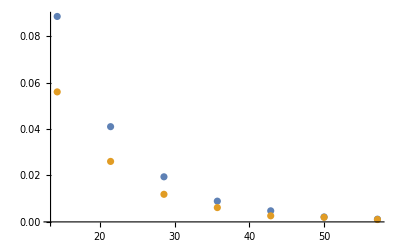

```mathematica
ListPlot[{Residualx1Data,Residualx2Data}]
```

```mathematica
LogResidualx1Data = {{14.286,Log[0.249- f[14.286]]},{21.429,Log[0.183-f[21.429]]},{28.571,Log[0.145-f[28.571]]},{35.714,Log[0.120-f[35.714]]},{42.857,Log[0.103-f[42.857]]},{50,Log[0.089-f[50]]},{57.143,Log[0.078-f[57.143]]}}
```

{{14.286,-2.42554},{21.429,-3.19432},{28.571,-3.94198},{35.714,-4.71839},{42.857,-5.34527},{50,-6.15296},{57.143,-6.75013}}

```mathematica
LogResidualx2Data = {{14.286,Log[0.05596218159845728]},{21.429,Log[0.026034832998461016]},{28.571,Log[0.011876561539305941]},{35.714,Log[0.0061616596755704744]},{42.857,Log[0.0026104283793260685]}}
```

{{14.286,-2.88308},{21.429,-3.64832},{28.571,-4.43319},{35.714,-5.08941},{42.857,-5.94824}}

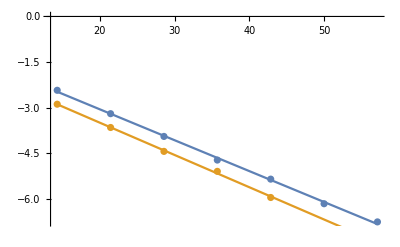

```mathematica
Show[ListPlot[{LogResidualx1Data,LogResidualx2Data}],Plot[{x1lineλ2,x2lineλ2},{t,14.286,57.143}]]
```

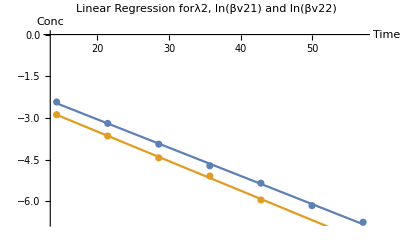

```mathematica
Show[%42,AxesLabel->{HoldForm[Time],HoldForm[Conc]},PlotLabel->RawBoxes[RowBox[{RowBox[{"Linear"," ","Regression"," ","forλ2"}],","," ",RowBox[{"ln",RowBox[{"(","βv21",")"}]," ","and"," ","ln",RowBox[{"(","βv22",")"}]}]}]],LabelStyle->{GrayLevel[0]}]
```

```mathematica
x1lineλ2=Normal[LinearModelFit[LogResidualx1Data,t,t]]
```

-1.02293-0.101472 t

```mathematica
Exp[-1.02293]
```

0.35954

```mathematica
x2lineλ2=Normal[LinearModelFit[LogResidualx2Data,t,t]]
```

-1.37182-0.106002 t

```mathematica
Exp[-1.37182]
```

0.253645

Question 3: 
Assume that the eigenvalues and the corresponding eigenvector of K are know. Show that the entries of the matrix K must satisfy the following equations.

```mathematica
Quit[]
```

```mathematica
x1[t_]=Exp[-0.017*t]
```

ⅇ^(-0.017 t)

```mathematica
x2[t_]=Exp[-0.11*t]
```

ⅇ^(-0.11 t)

```mathematica
EigenvalueEquations = {{x1[0],x2[0]},{x1[7.143],x2[7.143]},{x1[14.286],x2[14.286]},{x1[21.429],x2[21.429]},{x1[28.571],x2[28.571]},{x1[35.714],x2[35.714]},{x1[42.857],x2[42.857]},{x1[50],x2[50]},{x1[57.143],x2[57.143]},{x1[64.286],x2[64.286]},{x1[71.429],x2[71.429]},{x1[78.571],x2[78.571]},{x1[85.714],x2[85.714]},{x1[92.857],x2[92.857]},{x1[100],x2[100]}}
```

{{1.,1.},{0.885652,0.455787},{0.78438,0.207742},{0.694688,0.0946859},{0.615262,0.0431613},{0.544908,0.0196724},{0.482599,0.00896641},{0.427415,0.00408677},{0.378541,0.0018627},{0.335256,0.000848993},{0.29692,0.00038696},{0.262972,0.000176391},{0.232902,0.0000803965},{0.20627,0.0000366437},{0.182684,0.0000167017}}

```mathematica
x1 = {0.623,0.374,0.249,0.183,0.145,0.120,0.103,0.089,0.078,0.068,0.060,0.053,0.047,0.041,0.037}
```

{0.623,0.374,0.249,0.183,0.145,0.12,0.103,0.089,0.078,0.068,0.06,0.053,0.047,0.041,0.037}

```mathematica
solV11andV12=LeastSquares[EigenvalueEquations,x1]//MatrixForm
```

(0.205314
0.418607)

```mathematica
x2={0,0.113,0.151,0.157,0.150,0.137,0.124,0.110,0.098,0.087,0.077,0.068,0.060,0.053,0.047}
```

{0,0.113,0.151,0.157,0.15,0.137,0.124,0.11,0.098,0.087,0.077,0.068,0.06,0.053,0.047}

```mathematica
solv21andv22 = LeastSquares[EigenvalueEquations,x2]//MatrixForm
```

(0.261026
-0.260609)

```mathematica
VMatrix = {{0.205314,0.418607},{0.261026,-0.260609}}//MatrixForm
```

(0.205314 | 0.418607
0.261026 | -0.260609)

```mathematica
EigenvalueMatrix = {{-0.017,0},{0,-0.11}}//MatrixForm
```

(-0.017 | 0
0 | -0.11)

```mathematica
InverseVMatrix = Inverse[{{0.205314,0.418607},{0.261026,-0.260609}}]
```

{{1.60105,2.57171},{1.60361,-1.26134}}

```mathematica
K=Dot[{{0.205314,0.418607},{0.261026,-0.260609}},{{-0.017,0},{0,-0.11}},{{1.6010482067210876,2.571706988902511},{1.6036100411251284,-1.2613440499550412}}]//MatrixForm
```

(-0.0794293 | 0.0491047
0.0388661 | -0.0475707)

Question 4:
Given the estimates of OverHat[K_ij] of the entries of K and estimates OverHat[λ_1] and (λ̂)_2 of the eigenvalues of K , show how to obtain an estimate of (k̂)_01 of k_01 using the relations in Problem 1(b).

```mathematica
K
```

(-0.0794293 | 0.0491047
0.0388661 | -0.0475707)

```mathematica
k12 = 0.048
```

0.048

```mathematica
k21 = 0.0388661
```

0.0388661

```mathematica
k01=-(-0.0794293)-k21
```

0.0405632

```mathematica
-k21 - (-0.0792293)
```

0.0403632

```mathematica
-(k01+k12+k21)
```

-0.127429

```mathematica
-0.017+-0.11
```

-0.127

```mathematica
k12*k01
```

0.00194703

```mathematica
-0.017*-0.11
```

0.00187

Question 5:
Table 3.P.1 lists drug concentration measurements made in blood and tissue compartments over a period of 100 minutes. Use the method described in Problem 2 through 4 to estimate the rate coefficients k01, k12, and k21 in the system model from line 1 of table 3.P.1. Verify the accuracy of your estimates by plotting the solution components and the data in Table 3.P.1 on the same set of coordinate axes.

```mathematica
sol = Expand[DSolve[{x1'[t]==-0.0794293*x1[t]+0.048*x2[t],x2'[t]==0.0388661*x1[t]-0.048*x2[t],x1[0]==0.623,x2[0]==0}, {x1[t],x2[t]},t]]
```

{{x1[t]→0.418003 ⅇ^(-0.109677 t)+0.204997 ⅇ^(-0.0177525 t),x2[t]→-0.263408 ⅇ^(-0.109677 t)+0.263408 ⅇ^(-0.0177525 t)}}

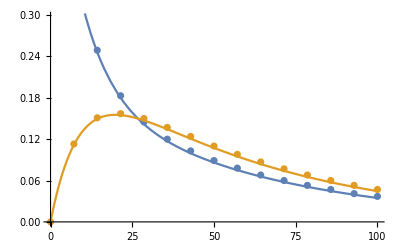

```mathematica
Show[ListPlot[{x1data,x2data}],Plot[{0.4180030483040753 ⅇ^(-0.10967684125131547 t)+0.20499695169592466 ⅇ^(-0.01775245874868453 t),-0.2634075926406902 ⅇ^(-0.10967684125131547 t)+0.2634075926406902 ⅇ^(-0.01775245874868453 t)},{t,0,100}]]
```

```mathematica
Show[%11,AxesLabel->{HoldForm[Time],HoldForm[Conc]},PlotLabel->HoldForm[Compartment Concentration Data with System Model],LabelStyle->{GrayLevel[0]}]
```